# 关于复数的解方程

```mathematica
Solve[Sin[x]==2,x,Complexes]
```

{{x→ConditionalExpression[π-ArcSin[2]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcSin[2]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Simplify[TrigToExp[ArcSin[2]]]
```

-ⅈ Log[ⅈ (2+√3)]

```mathematica
Sin[-ⅈ Log[ⅈ (2+√3)]]
```

-(-1-(2+√3)^2)/(2 (2+√3))

```mathematica
RootReduce[-(-1-(2+√3)^2)/(2 (2+√3))]
```

2

### ArcSin

```mathematica
Simplify[TrigToExp[ArcSin[x]]]
```

-ⅈ Log[ⅈ x+√(1-x^2)]

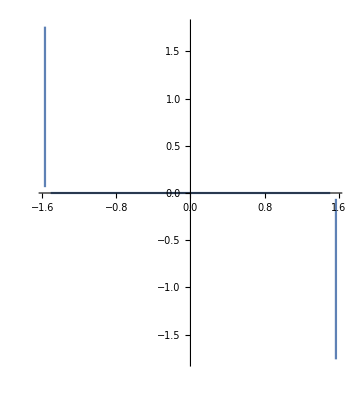

```mathematica
ParametricPlot[ReIm[-ⅈ Log[ⅈ x+√(1-x^2)]],{x,-3,3}]
```

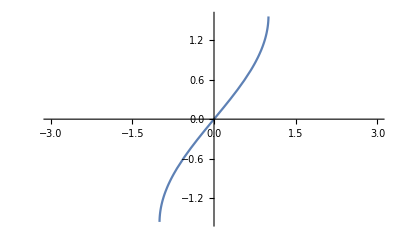

```mathematica
Plot[ArcSin[x],{x,-3,3}]
```

```mathematica
Manipulate[Graphics[{PointSize[Large],Magenta,Point@ReIm@Sin[Complex@@p]},Axes->True,PlotRange->5,GridLines->Automatic,GridLinesStyle->Directive[Orange, Dashed]],{{p,{0,0}},Locator}]
```